```mathematica
Clear[l];
$Assumptions=ly≥0&&ly∈Integers;
```

```mathematica
L=0;M=0;
l=1;m=0;
q=0;
Integrate[SphericalHarmonicY[1,q,θr,ϕr] SphericalHarmonicY[L,M,θr,ϕr] SphericalHarmonicY[l,m,θr,ϕr] Sin[θr],{θr,0,Pi},{ϕr,0,2 Pi}]
```

1/(2 √π)

```mathematica
Sqrt[(2 l+1) (2 L+1) (2+1)/(4 Pi)] ThreeJSymbol[{1,q},{L,M},{l,m}] ThreeJSymbol[{1,0},{L,0},{l,0}]
```

1/(2 √π)

```mathematica
wig[l_]:=(2 l-3) (ThreeJSymbol[{1,0},{l-1,0},{l,0}])^2
mine[l_]:=(1-3/(2 l))/(1-1/(4 l^2))
```

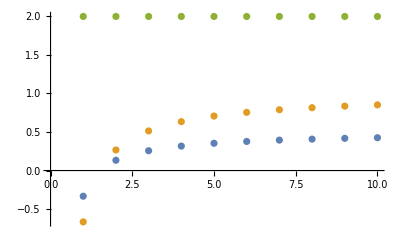

```mathematica
ListPlot[{Table[wig[jj],{jj,1,10}],Table[mine[jj],{jj,1,10}],Table[mine[jj]/wig[jj],{jj,1,10}]}]
```

```mathematica
w3j0[j1_,j2_,j3_]:=Module[{J=j1+j2+j3},
(-1)^(J/2) Sqrt[(J-2 j1)! (J-2 j2)! (J-2 j3)!/(J+1)!] (J/2)!/((J/2- j1)! (J/2- j2)! (J/2- j3)!)
]
```

```mathematica
ll=1;
(2 ll-3) w3j0[1,ll-1,ll]^2
```

-1/3